```mathematica
"Форма при t = 180 ";
```

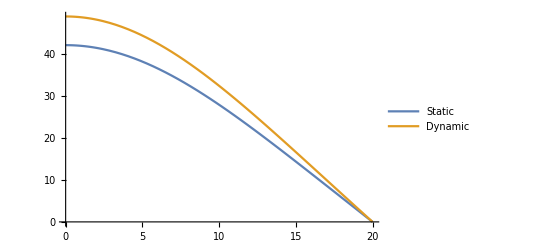

```mathematica
Plot[{displ⟦9⟧,W[180,r]},{r,RMin,RMax},PlotLegends->{"Static","Dynamic"}]
```

```mathematica
"Смещение при r = ~0";
```

```mathematica
centralDispl=Table[{ArrT⟦ii⟧,displ⟦ii⟧/.r->RMin},{ii,1,Length[ArrT]}];
```

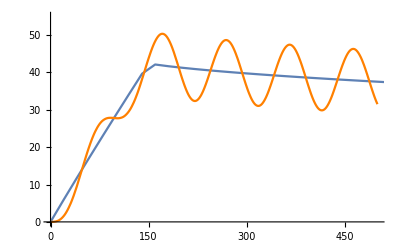

```mathematica
Show[ListLinePlot[centralDispl],Plot[W[t,RMin],{t,tMin,tMax},PlotStyle->Orange],PlotRange->{{0,tMax},{0,55}}]
```

```mathematica
"Кривизна при r = ~0";
```

```mathematica
centralCurv=Table[{ArrT⟦ii⟧,Abs[D[displ⟦ii⟧,{r,2}]]/.r->RMin},{ii,1,Length[ArrT]}];
```

```mathematica
curv [t_,r_]:=Evaluate[Abs[D[W[t,r],{r,2}]]]
```

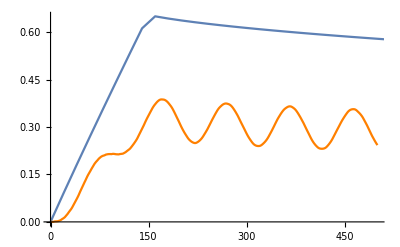

```mathematica
Show[ListLinePlot[centralCurv],Plot[curv[t,RMin],{t,tMin,tMax},PlotStyle->Orange],PlotRange->{{0,tMax},{0,0.65}}]
```